# Gyrobifastigium

### Author

Eric W. Weisstein
August 21, 2023

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polyhedra/Gyrobifastigium.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Gyrobifastigium.html.

©2023 Wolfram Research, Inc. except for portions noted otherwise

## Graphic

```mathematica
Complement[PolyhedronData["*Gyrobifastigium"],PolyhedronData["*ElongatedGyrobifastigium"]]
```

{CanonicalGyrobifastigium,EquilateralGyrobifastigium,PlesiohedralGyrobifastigium}

```mathematica
gyrobifastigia=%[[{2,3,1}]]
```

{EquilateralGyrobifastigium,PlesiohedralGyrobifastigium,CanonicalGyrobifastigium}

```mathematica
GraphicsRow[Graphics3D[{Opacity[.5],PolyhedronData[#,"Polyhedron"]},PlotLabel->Style[PolyhedronData[#,"Name"],Directive[Italic,Black,16,FontFamily->"Times"]],Boxed->False]&/@gyrobifastigia,Alignment->Top,Dividers->All,ImageSize->700]
```

-Graphics-

### Net

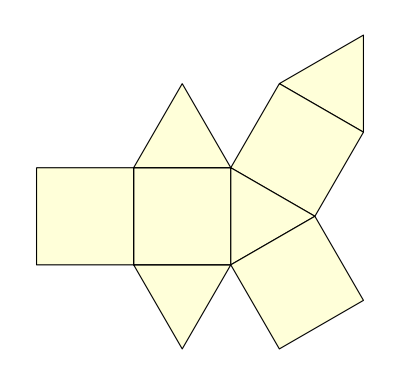

```mathematica
PolyhedronData["Gyrobifastigium","Net"]
```

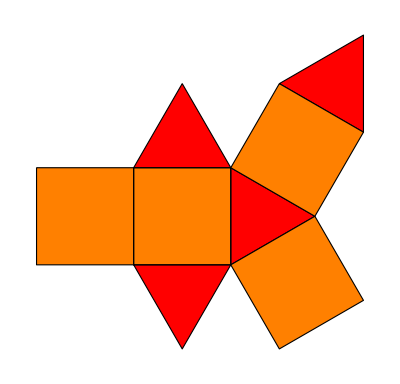

```mathematica
PolyhedronData["Gyrobifastigium","Net","Colored"]
```

```mathematica
NetPrintout[PolyhedronData["Gyrobifastigium","Polyhedron"],"Gyrobifastigium.pdf"]
```

## Properties

```mathematica
<<MathWorld`Polyhedroa`
```

```mathematica
p=PolyhedronData[pname="Gyrobifastigium","Polyhedron"]
```

Polyhedron[…]

```mathematica
vol=PolyhedronData[pname,"Volume"]
```

(√3)/2

### Centroid

```mathematica
PolyhedronData[pname,"Centroid"]
```

{0,0,0}

```mathematica
RegionCentroid[p]
```

{0,0,0}

```mathematica
PolyhedronCentroid[p]
```

{0,0,0}

### Circumsphere

```mathematica
PolyhedronData[pname,"Circumsphere"]
```

Missing[NotApplicable]

```mathematica
Circumsphere[p]
```

Circumsphere::indep: Circumsphere does not exist for ….

Circumsphere[Polyhedron[…]]

```mathematica
MyCircumsphere[p]
```

{}

### DihedralAngles

```mathematica
PolyhedronData[pname,"DihedralAngles"]//Tally
```

{{π/2,8},{(5 π)/6,4},{π/3,2}}

```mathematica
DihedralAngles[p]//FullSimplify//Tally
```

{{π/2,8},{(5 π)/6,4},{π/3,2}}

### EdgeLengths

```mathematica
PolyhedronData[pname,"EdgeLengths"]
```

{1}

```mathematica
PolyhedronData[pname,"Lines"]/.Line[l_]:>EuclideanDistance@@l//FullSimplify//Union
```

{1}

### Faces

### GeneralizedDiameter

```mathematica
PolyhedronData[pname,"GeneralizedDiameter"]
```

√(7/2)

```mathematica
GeneralizedDiameter[p]//FullSimplify
```

√(7/2)

### Insphere

```mathematica
PolyhedronData[pname,"Insphere"]
```

Missing[NotApplicable]

```mathematica
Insphere[p]
```

Insphere::indep: Insphere does not exist for ….

Insphere[Polyhedron[…]]

```mathematica
MyInsphere[p]
```

{}

### InertiaTensor

```mathematica
PolyhedronData[pname,"InertiaTensor"]
```

{{3/16,0,0},{0,3/16,0},{0,0,1/8}}

```mathematica
MomentOfInertia[p]/Volume[p]
```

{{3/16,0,0},{0,3/16,0},{0,0,1/8}}

```mathematica
PolyhedronInertiaTensor[p]
```

{{3/16,0,0},{0,3/16,0},{0,0,1/8}}

### MeanCylindricalRadius

```mathematica
PolyhedronData[pname,"MeanCylindricalRadius"]
```

1/24 (2+√2+5 ArcSinh[1])

```mathematica
NIntegrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.325878

```mathematica
(i=Integrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

$Aborted

```mathematica
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=MinMax/@Transpose[PolyhedronCoordinates[p]]
```

{{-1/2,1/2},{-1/2,1/2},{-(√3)/2,(√3)/2}}

```mathematica
ineq=PolyhedronData[pname,"RegionFunction"][x,y,z]
```

2 x≤1&&x≥-1/2&&2 z≤√3 (1+2 y)&&2 (√3 y+z)≤√3&&y≥-1/2&&2 y≤1&&√3+2 √3 x+2 z≥0&&2 √3 x≤√3+2 z

```mathematica
(i1=Integrate[Boole[ineq] √(x^2+y^2),{z,zmin,zmax}])//Timing
```

{0.275364,Piecewise[{{1/2 √3 √(x^2+y^2), (x==-1/2&&y==0)||(x==1/2&&y==0)}, {√3 √(x^2+y^2), x==0&&y==0}, {-((-√3+√3 x) √(x^2+y^2)), 0<x<1/2&&y==0}, {(√3+√3 x) √(x^2+y^2), -1/2<x<0&&y==0}, {-((-√3+√3 x-√3 y) √(x^2+y^2)), 0<x<1/2&&-1/2≤y<0}, {(√3+√3 x-√3 y) √(x^2+y^2), -1/2<x<0&&0<y≤1/2}, {-((-√3+√3 y) √(x^2+y^2)), x==0&&0<y≤1/2}, {(√3+√3 y) √(x^2+y^2), x==0&&-1/2≤y<0}, {-((-√3+√3 x+√3 y) √(x^2+y^2)), 0<x<1/2&&0<y≤1/2}, {(√3+√3 x+√3 y) √(x^2+y^2), -1/2<x<0&&-1/2≤y<0}, {-1/2 (-√3+2 √3 y) √(x^2+y^2), (x==-1/2&&0<y<1/2)||(x==1/2&&0<y<1/2)}, {1/2 (√3+2 √3 y) √(x^2+y^2), (x==-1/2&&-1/2<y<0)||(x==1/2&&-1/2<y<0)}, {0, True}}]}

```mathematica
NIntegrate[i1/vol,{x,xmin,xmax},{y,ymin,ymax}]
```

0.325878

```mathematica
(i2=Integrate[i1/vol,{x,xmin,xmax},{y,ymin,ymax}])//Timing
```

{24.3787,1/24 (2+√2+5 ArcSinh[1])}

```mathematica
N[i2]
```

0.325878

### MeanCylindricalSquareRadius

```mathematica
NIntegrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

0.125

```mathematica
(i=Integrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

{0.007119,1/8}

```mathematica
N[i]
```

0.125

### MeanSphericalRadius

```mathematica
NIntegrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

0.475274

```mathematica
(i=Integrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=MinMax/@Transpose[PolyhedronCoordinates[p]]
```

{{-1/2,1/2},{-1/2,1/2},{-(√3)/2,(√3)/2}}

```mathematica
ineq=PolyhedronData[pname,"RegionFunction"][x,y,z]
```

2 x≤1&&x≥-1/2&&2 z≤√3 (1+2 y)&&2 (√3 y+z)≤√3&&y≥-1/2&&2 y≤1&&√3+2 √3 x+2 z≥0&&2 √3 x≤√3+2 z

```mathematica
(i1=Integrate[Boole[ineq] √(x^2+y^2+z^2),{z,zmin,zmax}])//Timing
```

{56.9369,Piecewise[{{3/4, x==0&&y==0}, {1/8 (√3 √(3+4 x^2)+4 x^2 ArcSinh[(√3)/(2 Abs[x])]), (x==-1/2&&y==0)||(x==1/2&&y==0)}, {1/8 (√3 √(3+4 x^2-12 y+16 y^2)-2 √3 y √(3+4 x^2-12 y+16 y^2)+4 x^2 ArcTanh[(√3 (1-2 y))/(√(3+4 x^2+4 y (-3+4 y)))]+4 y^2 ArcTanh[(√3 (1-2 y))/(√(3+4 x^2+4 y (-3+4 y)))]), (x==-1/2&&0<y<1/2)||(x==1/2&&0<y<1/2)}, {1/8 (√3 √(3+4 x^2+12 y+16 y^2)+2 √3 y √(3+4 x^2+12 y+16 y^2)+4 x^2 ArcTanh[(√3 (1+2 y))/(√(3+4 x^2+4 y (3+4 y)))]+4 y^2 ArcTanh[(√3 (1+2 y))/(√(3+4 x^2+4 y (3+4 y)))]), (x==-1/2&&-1/2<y<0)||(x==1/2&&-1/2<y<0)}, {1/8 (√3 √(3+4 y^2)+√3 √(3-12 y+16 y^2)-2 √3 y √(3-12 y+16 y^2)+4 y^2 ArcTanh[(√3 (√(3+4 y^2)-2 y √(3+4 y^2)+√(3+4 y (-3+4 y))))/(3-6 y+√((3+4 y^2) (3+4 y (-3+4 y))))]), x==0&&0<y≤1/2}, {1/8 (√3 √(3+4 y^2)+√3 √(3+12 y+16 y^2)+2 √3 y √(3+12 y+16 y^2)+4 y^2 ArcTanh[(√3 (√(3+4 y^2)+2 y √(3+4 y^2)+√(3+4 y (3+4 y))))/(3+6 y+√((3+4 y^2) (3+4 y (3+4 y))))]), x==0&&-1/2≤y<0}, {1/8 (√3 √(3+4 x^2)+√3 √(3-12 x+16 x^2)-2 √3 x √(3-12 x+16 x^2)-2 x^2 Log[-√3+√(3+4 x^2)]+2 x^2 Log[√3+√(3+4 x^2)]+2 x^2 Log[√3-2 √3 x+√(3-12 x+16 x^2)]-2 x^2 Log[-√3+2 √3 x+√(3-12 x+16 x^2)]), 0<x<1/2&&y==0}, {1/8 (√3 √(3+4 x^2)+√3 √(3+12 x+16 x^2)+2 √3 x √(3+12 x+16 x^2)-2 x^2 Log[-√3+√(3+4 x^2)]+2 x^2 Log[√3+√(3+4 x^2)]-2 x^2 Log[-√3-2 √3 x+√(3+12 x+16 x^2)]+2 x^2 Log[√3+2 √3 x+√(3+12 x+16 x^2)]), -1/2<x<0&&y==0}, {1/8 (√3 √(3-12 x+16 x^2+4 y^2)-2 √3 x √(3-12 x+16 x^2+4 y^2)+√3 √(3+4 x^2-12 y+16 y^2)-2 √3 y √(3+4 x^2-12 y+16 y^2)+2 x^2 Log[√3-2 √3 x+√(3-12 x+16 x^2+4 y^2)]+2 y^2 Log[√3-2 √3 x+√(3-12 x+16 x^2+4 y^2)]-2 x^2 Log[-√3+2 √3 x+√(3-12 x+16 x^2+4 y^2)]-2 y^2 Log[-√3+2 √3 x+√(3-12 x+16 x^2+4 y^2)]+2 x^2 Log[√3-2 √3 y+√(3+4 x^2-12 y+16 y^2)]+2 y^2 Log[√3-2 √3 y+√(3+4 x^2-12 y+16 y^2)]-2 x^2 Log[-√3+2 √3 y+√(3+4 x^2-12 y+16 y^2)]-2 y^2 Log[-√3+2 √3 y+√(3+4 x^2-12 y+16 y^2)]), 0<x<1/2&&0<y≤1/2}, {1/8 (√3 √(3+12 x+16 x^2+4 y^2)+2 √3 x √(3+12 x+16 x^2+4 y^2)+√3 √(3+4 x^2-12 y+16 y^2)-2 √3 y √(3+4 x^2-12 y+16 y^2)-2 x^2 Log[-√3-2 √3 x+√(3+12 x+16 x^2+4 y^2)]-2 y^2 Log[-√3-2 √3 x+√(3+12 x+16 x^2+4 y^2)]+2 x^2 Log[√3+2 √3 x+√(3+12 x+16 x^2+4 y^2)]+2 y^2 Log[√3+2 √3 x+√(3+12 x+16 x^2+4 y^2)]+2 x^2 Log[√3-2 √3 y+√(3+4 x^2-12 y+16 y^2)]+2 y^2 Log[√3-2 √3 y+√(3+4 x^2-12 y+16 y^2)]-2 x^2 Log[-√3+2 √3 y+√(3+4 x^2-12 y+16 y^2)]-2 y^2 Log[-√3+2 √3 y+√(3+4 x^2-12 y+16 y^2)]), -1/2<x<0&&0<y≤1/2}, {1/8 (√3 √(3-12 x+16 x^2+4 y^2)-2 √3 x √(3-12 x+16 x^2+4 y^2)+√3 √(3+4 x^2+12 y+16 y^2)+2 √3 y √(3+4 x^2+12 y+16 y^2)+2 x^2 Log[√3-2 √3 x+√(3-12 x+16 x^2+4 y^2)]+2 y^2 Log[√3-2 √3 x+√(3-12 x+16 x^2+4 y^2)]-2 x^2 Log[-√3+2 √3 x+√(3-12 x+16 x^2+4 y^2)]-2 y^2 Log[-√3+2 √3 x+√(3-12 x+16 x^2+4 y^2)]-2 x^2 Log[-√3-2 √3 y+√(3+4 x^2+12 y+16 y^2)]-2 y^2 Log[-√3-2 √3 y+√(3+4 x^2+12 y+16 y^2)]+2 x^2 Log[√3+2 √3 y+√(3+4 x^2+12 y+16 y^2)]+2 y^2 Log[√3+2 √3 y+√(3+4 x^2+12 y+16 y^2)]), 0<x<1/2&&-1/2≤y<0}, {1/8 (√3 √(3+12 x+16 x^2+4 y^2)+2 √3 x √(3+12 x+16 x^2+4 y^2)+√3 √(3+4 x^2+12 y+16 y^2)+2 √3 y √(3+4 x^2+12 y+16 y^2)-2 x^2 Log[-√3-2 √3 x+√(3+12 x+16 x^2+4 y^2)]-2 y^2 Log[-√3-2 √3 x+√(3+12 x+16 x^2+4 y^2)]+2 x^2 Log[√3+2 √3 x+√(3+12 x+16 x^2+4 y^2)]+2 y^2 Log[√3+2 √3 x+√(3+12 x+16 x^2+4 y^2)]-2 x^2 Log[-√3-2 √3 y+√(3+4 x^2+12 y+16 y^2)]-2 y^2 Log[-√3-2 √3 y+√(3+4 x^2+12 y+16 y^2)]+2 x^2 Log[√3+2 √3 y+√(3+4 x^2+12 y+16 y^2)]+2 y^2 Log[√3+2 √3 y+√(3+4 x^2+12 y+16 y^2)]), -1/2<x<0&&-1/2≤y<0}, {0, True}}]}

```mathematica
NIntegrate[i1/vol,{x,xmin,xmax},{y,ymin,ymax}]
```

0.475274

```mathematica
(i2=Integrate[i1/vol,{x,xmin,xmax},{y,ymin,ymax}])//Timing
```

### MeanSphericalSquareRadius

```mathematica
NIntegrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

0.25

```mathematica
(i=Integrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

{0.00687,1/4}

```mathematica
N[i]
```

0.25

### Midsphere

```mathematica
PolyhedronData[pname,"Midsphere"]
```

Missing[NotApplicable]

```mathematica
Midsphere[p]
```

{}

### SurfaceArea

```mathematica
PolyhedronData[pname,"SurfaceArea"]
```

4+√3

```mathematica
SurfaceArea[p]//RootReduce
```

4+√3

```mathematica
Total[Area/@PolyhedronData[pname,"Polygons"]]
```

4+√3

### VertexSubsetHulls

#### Platonic

```mathematica
(h=VertexSubsetHulls[p,"Platonic","Skip"->{}])//Timing
```

Finding equilateral triangles...

Finding potential tetrahedra from equilateral triangles...

Finding tetrahedra from potential candidates...

Finding cubes from tetrahedra...

Finding dodecahedron from cubes...

Finding octahedra by building up from equilateral triangles...

Finding dodecahedra from octahedra...

Finding icosahedra by building up from equilateral triangles...

{0.005818,{}}

### Volume

```mathematica
PolyhedronData[pname,"Volume"]
```

(√3)/2

```mathematica
Volume[p]//FullSimplify
```

(√3)/2

```mathematica
PolyhedronVolume[p,Method->"GaussLaw"]//FullSimplify
```

(√3)/2

## Perspective projections

```mathematica
Manipulate[PolyhedronProjectionGraph[PolyhedronData["Cuboctahedron","Polyhedron"],{a,b,c}],{a,-1,1},{b,-1,1},{c,-1,1}]
```

### XXX

```mathematica
PolyhedronProjectionGraph[PolyhedronData["DuererSolid","Polyhedron"],]
```